```mathematica
A  =π*( 0.0095*.5)^2
P0 = (50/14.7+1)*10^5
V0 = .0015
γ = 7/5
ρ2 = 1000
ρ1 =1.22
P1 = 10^5
```

0.0000708822

440136.

0.0015

7/5

1000

1.22

100000

```mathematica
sol1 = NDSolve[{V'[t] == A*(Sqrt[2*(P0*(V0/(V[t])^γ) - P1)/ρ2]),V[0] == V0}, V[t], {t,0,1}]
```

{{V[t]→InterpolatingFunction[…][t]}}

```mathematica
V[t_] = V[t]/.sol1[[1]]
```

InterpolatingFunction[…][t]

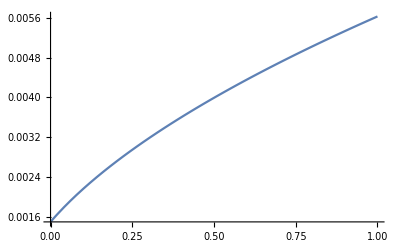

```mathematica
Plot[V[t], {t,0,1}]
```

```mathematica
V'[t_] == A*Sqrt[2*(P0*(V0/(Vol[t])^γ) - P1)/ρ2]
```

InterpolatingFunction[…][t_]==3.16995×10^-6 √(-100000+660.204/(InterpolatingFunction[…][t])^(7/5))

```mathematica
Clear[T]
```

```mathematica
T[t_]= (ρ1/A)*V'[t]^2
```

17211.7 (InterpolatingFunction[…][t])^2

```mathematica
Clear[Velocities]
```

```mathematica
g = 9.81
m[t_] =m0 -V'[t]*ρ2*t 
m0 = .6889
c = .2
A = π*( 0.0095*.5)^2
k = A*c*ρ1
ρ1 = 1.22
θ = .2
```

9.81

0.6889-1000 t InterpolatingFunction[…][t]

0.6889

0.2

0.0000708822

0.0000172953

1.22

0.2

```mathematica
Velocities = NDSolve[{m[t]*vy'[t]==Cos[θ]*T[t]-m[t]*g-.5*k*(vx[t]^2+vy[t]^2)*Cos[θ], (m[t])*vx'[t]==T[t]*Sin[θ]-.5*k*(vx[t]^2+vy[t]^2)*Sin[θ], vy[0]==3,vx[0]==0},{vy[t],vx[t]},{t,0,1}]
```

NDSolve::ndsz: At t == 0.121882, step size is effectively zero; singularity or stiff system suspected.

{{vy[t]→InterpolatingFunction[…][t],vx[t]→InterpolatingFunction[…][t]}}

9.81

0.6889-1000 t InterpolatingFunction[…][t]

0.6889

0.2

0.0000708822

0.0000172953

1.22

NDSolve::ndsz: At t == 0.238208, step size is effectively zero; singularity or stiff system suspected.

```mathematica
vxsol[t_] = vxsol[t]/.Velocities[[1]]
vysol[t_] = vysol[t]/.Velocities[[1]]
```

InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

```mathematica
hx[t_] = Integrate[vxsol[t],t]
hy[t_] = Integrate[vysol[t],t]
```

```mathematica
ax[t_]  = D[vxsol[t],t]
ay[t_] = D[vysol[t],t]
```

InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

«3 more identical outputs»

```mathematica
Plot[ax[t],{t,0,1}]
```

-Graphics-

NDSolve::dupv: Duplicate variable t found in NDSolve[{vy'[t]==5.29381 (-mg-0.0000172953 (Power[«2»]+Power[«2»]) Cos[θ] Sin[Times[«2»]]+Cos[θ] T[t]),vx'[t]==5.29381 (-0.0000172953 (Power[«2»]+Power[«2»]) Sin[Times[«2»]] Sin[θ]+Sin[θ] T[t]),vy[0]==0,vx[0]==0},vy[t],vx[t],{t,0,1},{t,0,1}].

```mathematica
Plot[ay[t],{t,0,.2}]
```

-Graphics-

```mathematica
Clear[V]
```

```mathematica
Clear[V]
```